# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
sqSKA = 30000
```

30000

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 sqSKA/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

# Magnification & Evolution Bias

### Population parameters

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bTzSKA:=bmeanzSKA ;
```

### EXTREME SPLITTING 10%-90% (m = 10)

```mathematica
m = 10;
```

```mathematica
db=1.4;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 1/10;
```

```mathematica
smodelBzSKA = List[1.03913831,0.71999785,0.70016622,0.80291617,0.80509085,0.86385634,0.93133131,0.99350429,1.04896737,1.0983242,1.14410701,1.18703114,1.23676623,1.29877001,1.36750798,1.44075302,1.51593195,1.59199958,1.66844103];
```

```mathematica
fevolBzSKA = List[-24.02362577,1.23631355,-1.68886235,-1.2314607,-0.25657339,-0.01563204,0.06640555,0.27155143,0.57179683,0.94187865,1.35648053,1.79696626,2.16686823,2.40966479,2.59808125,2.75955326,2.92184145,3.10220004,3.29514781];
```

```mathematica
bBzSKA = bB[m, dbz]
```

{1.88304,1.93379,1.98867,2.04801,2.11219,2.1816,2.25666,2.33784,2.42563,2.52056,2.62323,2.73426,2.85434,2.98419,3.12462,3.27649,3.44073,3.61834,3.81042}

#### Faint

```mathematica
nFSKA = 9/10;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA);]
```

```mathematica
m
```

10

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.00294009,0.106607,0.195446,0.289033,0.403431,0.512349,0.615682,0.716564,0.816123,0.915166,1.01556,1.11733,1.2213,1.32587,1.43275,1.54216,1.6543,1.7695,1.88453}

```mathematica
fevolFzSKA =List[5.17277222,2.54206913,2.22659099,1.46233479,0.60197595,-0.03827728,-0.50524214,-0.86241689,-1.14009535,-1.37570916,-1.57218441,-1.75009982,-1.90570711,-2.03785252,-2.15846779,-2.27053596,-2.37692272,-2.47268313,-2.54081985];
```

```mathematica
bFzSKA= bF[m, dbz]
```

{0.483042,0.533787,0.588665,0.648013,0.712194,0.781603,0.856665,0.93784,1.02563,1.12056,1.22323,1.33426,1.45434,1.58419,1.72462,1.87649,2.04073,2.21834,2.41042}

# Covariance

## Parameters

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
RedshifteBOSS = List[0.65,0.75,0.85,0.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NbareBOSS = NbarzSKAfint[RedshifteBOSS]
```

{0.0164978,0.0105573,0.00681219,0.00439079}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
sqeBOSS = 10000
```

10000

```mathematica
VzeBOSS=ParallelTable[4/3 Pi ( r[RedshifteBOSS[[i]]+0.05]^3-r[RedshifteBOSS[[i]]-0.05]^3)/H0^3 sqeBOSS/41253,{i,1,Length[RedshifteBOSS]}]
```

{1.7058×10^9,2.02261×10^9,2.31552×10^9,2.58111×10^9}

```mathematica
NtoteBOSS = Sum[NbareBOSS[[k]]VzeBOSS[[k]],{k,1,Length[RedshifteBOSS]}]
```

7.66021×10^7

```mathematica
(*nBSKA=1/m;*)
(*nFSKA=1-nBSKA;*)
nBzSKA=Table[nBSKA, {i,Length[zSKA]}];
nFzSKA=Table[nFSKA, {i,Length[zSKA]}];
```

```mathematica
nBzSKA
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

```mathematica
nFzSKA
```

{9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10}

```mathematica
NbarBzSKA=NbarzSKA*nBzSKA
```

{0.0200168,0.0117195,0.00697361,0.00422937,0.00260542,0.00164978,0.00105573,0.000681219,0.000439079,0.000280882,0.000179506,0.000113967,0.0000716732,0.0000448765,0.0000276039,0.0000167883,0.000010073,5.9082×10^-6,3.38995×10^-6}

```mathematica
NbarFzSKA=NbarzSKA*nFzSKA
```

{0.180152,0.105476,0.0627625,0.0380643,0.0234488,0.014848,0.00950155,0.00613097,0.00395171,0.00252793,0.00161555,0.0010257,0.000645059,0.000403888,0.000248435,0.000151095,0.000090657,0.0000531738,0.0000305096}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA /nBzSKA
```

{8.70241×10^-8,5.45636×10^-8,4.72637×10^-8,4.76986×10^-8,5.25955×10^-8,6.05173×10^-8,7.2461×10^-8,8.93679×10^-8,1.13643×10^-7,1.49076×10^-7,1.99537×10^-7,2.73143×10^-7,3.82531×10^-7,5.44219×10^-7,7.95805×10^-7,1.18687×10^-6,1.80744×10^-6,2.83384×10^-6,4.56788×10^-6}

```mathematica
coeffFSKA/nFzSKA
```

{9.66934×10^-9,6.06263×10^-9,5.25153×10^-9,5.29984×10^-9,5.84395×10^-9,6.72415×10^-9,8.05123×10^-9,9.92976×10^-9,1.26271×10^-8,1.6564×10^-8,2.21708×10^-8,3.03493×10^-8,4.25035×10^-8,6.04688×10^-8,8.84228×10^-8,1.31874×10^-7,2.00827×10^-7,3.14871×10^-7,5.07542×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

SET FEVOL =  0 MANUALLY

```mathematica
(*fevolBzSKA = Table[0.,{i,1,ktot}];
fevolFzSKA = Table[0.,{i,1,ktot}];*)
```

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA=(5smodelBzSKA +(2-5smodelBzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA)fzSKA
```

{3.67453,-3.17161,0.108577,-0.235995,-0.390502,-0.404636,-0.326334,-0.320991,-0.377902,-0.489366,-0.644755,-0.830883,-0.966863,-0.992326,-0.961212,-0.89451,-0.817281,-0.746799,-0.679258}

```mathematica
cFzSKA=(5smodelFzSKA +(2-5smodelFzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA)fzSKA
```

{6.12652,3.38699,1.78131,1.24643,1.10954,1.14335,1.26066,1.43127,1.63733,1.88406,2.15468,2.4572,2.77995,3.11702,3.47367,3.84958,4.24514,4.65398,5.05611}

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=corrCC[n,m]Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

```mathematica
coeffvarianceCC[1,1,bL,bM,bL,bM,f]
```

0

```mathematica
coeffcovCCrel[1,1,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

2/5 (bM cL-bL cM)^2+4/7 (cL-cM) (bM cL-bL cM) f+2/9 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[3,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

46/315 (bM cL-bL cM)^2+52/231 (cL-cM) (bM cL-bL cM) f+14/143 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[1,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

-21 (4/35 (bM cL-bL cM)^2+16/63 (cL-cM) (bM cL-bL cM) f+4/33 (cL-cM)^2 f^2)

```mathematica
corrCC[3,3]
```

1

```mathematica
corrCC[1,3]
```

-21

```mathematica
corrCC[1,3]coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

441 (4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2)

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

```mathematica
coeffvarCC00=coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

Monopole - 1 Population

```mathematica
coeffvarCC[0,0,B,B,B,B,f]
```

B^4+(4 B^3 f)/3+(6 B^2 f^2)/5+(4 B f^3)/7+f^4/9

```mathematica
coeffvarCC1pop00BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{2.94842×10^-8,1.11071×10^-8,5.87415×10^-9,3.69339×10^-9,2.58353×10^-9,1.94528×10^-9,1.54739×10^-9,1.28532×10^-9,1.10626×10^-9,9.81257×10^-10,8.93462×10^-10,8.32606×10^-10,7.92249×10^-10,7.68305×10^-10,7.58217×10^-10,7.60477×10^-10,7.74351×10^-10,7.99718×10^-10,8.3699×10^-10}

```mathematica
coeffvarCC1pop00FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.86632×10^-10,2.31318×10^-10,1.50437×10^-10,1.13967×10^-10,9.45247×10^-11,8.33346×10^-11,7.68498×10^-11,7.34208×10^-11,7.22182×10^-11,7.2819×10^-11,7.50289×10^-11,7.87997×10^-11,8.4191×10^-11,9.13538×10^-11,1.00528×10^-10,1.12048×10^-10,1.26357×10^-10,1.44028×10^-10,1.6579×10^-10}

```mathematica
varCCMONOBrightLp4d4to172zSKA=Table[coeffvarCC1pop00BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOFaintLp4d4to172zSKA=Table[coeffvarCC1pop00FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
coeffvarCC1pop00BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.59629×10^-9,1.5289×10^-9,9.00919×10^-10,6.24692×10^-10,4.77958×10^-10,3.91061×10^-10,3.36244×10^-10,3.00603×10^-10,2.77474×10^-10,2.63163×10^-10,2.55538×10^-10,2.5336×10^-10,2.55941×10^-10,2.62971×10^-10,2.74417×10^-10,2.90478×10^-10,3.11567×10^-10,3.38311×10^-10,3.71573×10^-10}

```mathematica
varCCMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCC1pop00BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,B,F,B,F,f]
```

f^4/9+B^2 F^2+2/7 f^3 (B+F)+2/3 B f F (B+F)+1/5 f^2 (B^2+4 B F+F^2)

```mathematica
coeffvarCC2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.59629×10^-9,1.5289×10^-9,9.00919×10^-10,6.24692×10^-10,4.77958×10^-10,3.91061×10^-10,3.36244×10^-10,3.00603×10^-10,2.77474×10^-10,2.63163×10^-10,2.55538×10^-10,2.5336×10^-10,2.55941×10^-10,2.62971×10^-10,2.74417×10^-10,2.90478×10^-10,3.11567×10^-10,3.38311×10^-10,3.71573×10^-10}

```mathematica
varCCMONO2popLp4d4to172zSKA=Table[coeffvarCC2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCCBright2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.01513×10^-8,4.06785×10^-9,2.27396×10^-9,1.50348×10^-9,1.10131×10^-9,8.65447×10^-10,7.16523×10^-10,6.18063×10^-10,5.51378×10^-10,5.06115×10^-10,4.76214×10^-10,4.58011×10^-10,4.49265×10^-10,4.48647×10^-10,4.55448×10^-10,4.69422×10^-10,4.90697×10^-10,5.19735×10^-10,5.57325×10^-10}

```mathematica
coeffvarCCFaint2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.30772×10^-9,5.88446×10^-10,3.64637×10^-10,2.64537×10^-10,2.10931×10^-10,1.79308×10^-10,1.59802×10^-10,1.47802×10^-10,1.40935×10^-10,1.37912×10^-10,1.38027×10^-10,1.40921×10^-10,1.46468×10^-10,1.54712×10^-10,1.65844×10^-10,1.8019×10^-10,1.9822×10^-10,2.20566×10^-10,2.48044×10^-10}

```mathematica
varCCMONOBrigth2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONOFaint2popLp4d4to172zSKA= Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffvarCC[1,1,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,1,B,F,B,F,cB,cF,cB,cF,f]
```

2/9 (cB-cF)^2 f^2+2/5 (B cF-cB F)^2+4/7 (cB-cF) f (-B cF+cB F)

```mathematica
coeffvarCC11relzSKA=coeffvarCCrelSKAz[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.53316×10^-8,5.26353×10^-9,3.4027×10^-10,1.19908×10^-10,7.11241×10^-11,5.37372×10^-11,4.5298×10^-11,4.45524×10^-11,4.7957×10^-11,5.50758×10^-11,6.48473×10^-11,7.76572×10^-11,9.07299×10^-11,1.0179×10^-10,1.1285×10^-10,1.24689×10^-10,1.38394×10^-10,1.54549×10^-10,1.72145×10^-10}

```mathematica
varCCDIPrelLp4d4to172zSKA=Table[coeffvarCC11relzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

#### Quadrupole

```mathematica
coeffvarCC[2,2,B,B,B,B,f]
```

B^4/5+(44 B^3 f)/105+(18 B^2 f^2)/35+(68 B f^3)/231+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCC1pop22BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{7.47636×10^-9,2.849×10^-9,1.51937×10^-9,9.60623×10^-10,6.74032×10^-10,5.08005×10^-10,4.03754×10^-10,3.34574×10^-10,2.86907×10^-10,2.53281×10^-10,2.2932×10^-10,2.12339×10^-10,2.00639×10^-10,1.93127×10^-10,1.89102×10^-10,1.8813×10^-10,1.89974×10^-10,1.94547×10^-10,2.01889×10^-10}

```mathematica
coeffvarCC1pop22FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.8597×10^-10,8.779×10^-11,5.64764×10^-11,4.21846×10^-11,3.4405×10^-11,2.97617×10^-11,2.68829×10^-11,2.51227×10^-11,2.41478×10^-11,2.37777×10^-11,2.39158×10^-11,2.45167×10^-11,2.55705×10^-11,2.70941×10^-11,2.9129×10^-11,3.17404×10^-11,3.50191×10^-11,3.90856×10^-11,4.40952×10^-11}

```mathematica
varCCQUADBrightLp4d4to172zSKA= Table[coeffvarCC1pop22BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaintLp4d4to172zSKA= Table[coeffvarCC1pop22FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC1pop22BFzSKA = coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.13471×10^-9,4.82994×10^-10,2.83867×10^-10,1.95699×10^-10,1.48484×10^-10,1.20225×10^-10,1.02128×10^-10,9.00868×10^-11,8.19672×10^-11,7.65745×10^-11,7.32063×10^-11,7.144×10^-11,7.10242×10^-11,7.18209×10^-11,7.37729×10^-11,7.68869×10^-11,8.12248×10^-11,8.69017×10^-11,9.40872×10^-11}

```mathematica
varCCQUADBrightFaintLp4d4to172zSKA = Table[coeffvarCC1pop22BFzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.13471×10^-9,4.82994×10^-10,2.83867×10^-10,1.95699×10^-10,1.48484×10^-10,1.20225×10^-10,1.02128×10^-10,9.00868×10^-11,8.19672×10^-11,7.65745×10^-11,7.32063×10^-11,7.144×10^-11,7.10242×10^-11,7.18209×10^-11,7.37729×10^-11,7.68869×10^-11,8.12248×10^-11,8.69017×10^-11,9.40872×10^-11}

```mathematica
varCCQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.87578×10^-9,1.15973×10^-9,6.5009×10^-10,4.29698×10^-10,3.13865×10^-10,2.45428×10^-10,2.01843×10^-10,1.72707×10^-10,1.52664×10^-10,1.3873×10^-10,1.29143×10^-10,1.22823×10^-10,1.19096×10^-10,1.17543×10^-10,1.17921×10^-10,1.20108×10^-10,1.24083×10^-10,1.29907×10^-10,1.37722×10^-10}

```mathematica
coeffvarCCFaint2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.56249×10^-10,2.04627×10^-10,1.25886×10^-10,9.03786×10^-11,7.11284×10^-11,5.95536×10^-11,5.21883×10^-11,4.74025×10^-11,4.43468×10^-11,4.25489×10^-11,4.17376×10^-11,4.17592×10^-11,4.25354×10^-11,4.4041×10^-11,4.62925×10^-11,4.93429×10^-11,5.3281×10^-11,5.8233×10^-11,6.43679×10^-11}

```mathematica
varCCQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffvarCC[3,3,b,b,b,b,f]
```

0

```mathematica
coeffcovCCrel[3,3,B,F,B,F,cB,cF,cB,cF,f]
```

14/143 (cB-cF)^2 f^2+46/315 (B cF-cB F)^2+52/231 (cB-cF) f (-B cF+cB F)

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.19258×10^-26,-3.63141×10^-26,-8.99628×10^-27,-3.49297×10^-27,-2.51324×10^-27,1.90251×10^-27,1.00561×10^-26,-6.6546×10^-27,-2.3746×10^-27,5.64439×10^-27,2.30395×10^-27,6.39183×10^-28,3.75855×10^-27,5.85332×10^-27,5.0369×10^-27,-2.50235×10^-27,-1.18016×10^-27,2.07317×10^-27,-3.08119×10^-27}

```mathematica
coeffvarCC33relzSKA=coeffvarCCrelSKAz[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{5.68797×10^-9,2.0133×10^-9,1.28344×10^-10,4.5472×10^-11,2.70475×10^-11,2.04343×10^-11,1.71969×10^-11,1.68977×10^-11,1.81792×10^-11,2.08691×10^-11,2.45603×10^-11,2.93931×10^-11,3.43053×10^-11,3.84316×10^-11,4.25415×10^-11,4.6931×10^-11,5.20107×10^-11,5.79994×10^-11,6.45154×10^-11}

```mathematica
varCCOCTrelLp4d4to172zSKA=Table[coeffvarCC33relzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

46/315 (bM cL-bL cM) (bP cN-bN cP)-26/231 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+14/143 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[3,3,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
Diagonal[varCCOCTrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.02595×10^-12,9.36244×10^-12,2.98856×10^-11,6.34372×10^-11,1.0868×10^-10,1.63428×10^-10,2.25322×10^-10,2.92152×10^-10,3.62001×10^-10,4.33292×10^-10,5.04924×10^-10,5.76299×10^-10,6.46393×10^-10,7.13725×10^-10,7.75533×10^-10}

```mathematica
Diagonal[varCCDIPrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.95886×10^-10,6.16637×10^-10,1.10091×10^-9,1.57283×10^-9,1.9994×10^-9,2.36862×10^-9,2.67882×10^-9,2.93328×10^-9,3.13753×10^-9,3.29794×10^-9,3.42118×10^-9,3.51412×10^-9,3.58359×10^-9,3.63524×10^-9,3.6723×10^-9}

```mathematica
Diagonal[varCCQUADBrightLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.000013249,0.0000287526,0.0000393829,0.0000457426,0.0000490412,0.000050263,0.0000501147,0.0000490859,0.0000475141,0.0000456502,0.0000436738,0.0000416704,0.0000394904,0.0000369962,0.0000343792}

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,B,B,B,B,f]
```

B^4/9+(52 B^3 f)/231+(1286 B^2 f^2)/5005+(436 B f^3)/3003+(79 f^4)/2431

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCCtotpop44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXAtotpopLp4d4to172zSKA=Table[coeffvarCCtotpop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC[0,2,B,B,B,B,f]
```

-5 ((8 B^3 f)/15+(24 B^2 f^2)/35+(8 B f^3)/21+(8 f^4)/99)

```mathematica
coeffvarCC1pop02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-2.41052×10^-8,-9.52125×10^-9,-5.20498×10^-9,-3.34345×10^-9,-2.36631×10^-9,-1.7882×10^-9,-1.4179×10^-9,-1.16716×10^-9,-9.90497×10^-10,-8.62452×10^-10,-7.67845×10^-10,-6.97176×10^-10,-6.44276×10^-10,-6.05014×10^-10,-5.76576×10^-10,-5.5702×10^-10,-5.45007×10^-10,-5.39635×10^-10,-5.40325×10^-10}

```mathematica
coeffvarCC1pop02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.10426×10^-9,-5.19146×10^-10,-3.31742×10^-10,-2.45526×10^-10,-1.97927×10^-10,-1.68807×10^-10,-1.49949×10^-10,-1.37444×10^-10,-1.29227×10^-10,-1.24127×10^-10,-1.21448×10^-10,-1.20772×10^-10,-1.21851×10^-10,-1.24554×10^-10,-1.28833×10^-10,-1.34707×10^-10,-1.42251×10^-10,-1.51593×10^-10,-1.62913×10^-10}

```mathematica
varCCMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCC1pop02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaintLp4d4to172zSKA=Table[coeffvarCC1pop02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC02BrightFaint=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-5.77248×10^-9,-2.45757×10^-9,-1.43792×10^-9,-9.82977×10^-10,-7.36987×10^-10,-5.8781×10^-10,-4.90444×10^-10,-4.23766×10^-10,-3.76707×10^-10,-3.42979×10^-10,-3.18795×10^-10,-3.01768×10^-10,-2.90352×10^-10,-2.83531×10^-10,-2.8064×10^-10,-2.81258×10^-10,-2.85144×10^-10,-2.92196×10^-10,-3.0243×10^-10}

```mathematica
varCCMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCC02BrightFaint[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,B,F,B,F,f]
```

-5 ((8 f^4)/99+4/21 f^3 (B+F)+4/15 B f F (B+F)+4/35 f^2 (B^2+4 B F+F^2))

```mathematica
coeffvarCC2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-5.77248×10^-9,-2.45757×10^-9,-1.43792×10^-9,-9.82977×10^-10,-7.36987×10^-10,-5.8781×10^-10,-4.90444×10^-10,-4.23766×10^-10,-3.76707×10^-10,-3.42979×10^-10,-3.18795×10^-10,-3.01768×10^-10,-2.90352×10^-10,-2.83531×10^-10,-2.8064×10^-10,-2.81258×10^-10,-2.85144×10^-10,-2.92196×10^-10,-3.0243×10^-10}

```mathematica
varCCMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.24028×10^-8,-5.05294×10^-9,-2.84238×10^-9,-1.87507×10^-9,-1.36066×10^-9,-1.05288×10^-9,-8.53929×10^-10,-7.18346×10^-10,-6.22529×10^-10,-5.53175×10^-10,-5.02311×10^-10,-4.64928×10^-10,-4.37767×10^-10,-4.18656×10^-10,-4.06128×10^-10,-3.99193×10^-10,-3.97201×10^-10,-3.99751×10^-10,-4.06635×10^-10}

```mathematica
coeffvarCCFaint2pop02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.55833×10^-9,-1.14351×10^-9,-6.98681×10^-10,-4.96643×10^-10,-3.85877×10^-10,-3.18086×10^-10,-2.73699×10^-10,-2.43453×10^-10,-2.22462×10^-10,-2.07939×10^-10,-1.98204×10^-10,-1.92211×10^-10,-1.89292×10^-10,-1.89033×10^-10,-1.91185×10^-10,-1.95626×10^-10,-2.02329×10^-10,-2.11351×10^-10,-2.2282×10^-10}

```mathematica
varCCMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,B,T,T,f]
```

9 ((16 f^4)/429+16/231 f^3 (B+T)+8/315 f^2 (B^2+4 B T+T^2))

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC1pop04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.67954×10^-9,7.16845×10^-10,4.16794×10^-10,2.81066×10^-10,2.06593×10^-10,1.60693×10^-10,1.30163×10^-10,1.08757×10^-10,9.31674×10^-11,8.14952×10^-11,7.2576×10^-11,6.56607×10^-11,6.02476×10^-11,5.59904×10^-11,5.26439×10^-11,5.00309×10^-11,4.80218×10^-11,4.65204×10^-11,4.54553×10^-11}

```mathematica
coeffvarCC1pop04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{5.29873×10^-10,2.42586×10^-10,1.50176×10^-10,1.07186×10^-10,8.29894×10^-11,6.77336×10^-11,5.73886×10^-11,5.00247×10^-11,4.46088×10^-11,4.05398×10^-11,3.74451×10^-11,3.50823×10^-11,3.32873×10^-11,3.19463×10^-11,3.09785×10^-11,3.03256×10^-11,2.99459×10^-11,2.98091×10^-11,2.9894×10^-11}

```mathematica
varCCMONOHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,F,T,T,f]
```

9 ((16 f^4)/429+8/231 f^3 (B+F+2 T)+8/315 f^2 (T (2 F+T)+B (F+2 T)))

```mathematica
coeffvarCC2pop04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{9.81249×10^-10,4.32008×10^-10,2.5829×10^-10,1.78657×10^-10,1.34422×10^-10,1.06851×10^-10,8.83314×10^-11,7.52384×10^-11,6.56439×10^-11,5.84323×10^-11,5.29164×10^-11,4.86509×10^-11,4.53365×10^-11,4.27654×10^-11,4.07902×10^-11,3.93044×10^-11,3.823×10^-11,3.75099×10^-11,3.71022×10^-11}

```mathematica
varCCMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC[2,4,B,B,T,T,f]
```

-45 ((16 f^4)/429+(232 f^3 (B+T))/3003+8/105 B f T (B+T)+(136 f^2 (B^2+4 B T+T^2))/3465)

```mathematica
coeffvarCC1pop24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-2.07898×10^-8,-8.73185×10^-9,-5.04382×10^-9,-3.40562×10^-9,-2.52278×10^-9,-1.98848×10^-9,-1.63992×10^-9,-1.40082×10^-9,-1.23127×10^-9,-1.10865×10^-9,-1.0193×10^-9,-9.54615×10^-10,-9.08974×10^-10,-8.78648×10^-10,-8.61145×10^-10,-8.54823×10^-10,-8.58656×10^-10,-8.72084×10^-10,-8.94921×10^-10}

```mathematica
coeffvarCC1pop24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-4.44318×10^-9,-2.04454×10^-9,-1.28034×10^-9,-9.2947×10^-10,-7.35448×10^-10,-6.16012×10^-10,-5.37656×10^-10,-4.84449×10^-10,-4.47958×10^-10,-4.23365×10^-10,-4.07775×10^-10,-3.99392×10^-10,-3.97099×10^-10,-4.00227×10^-10,-4.08418×10^-10,-4.21554×10^-10,-4.39705×10^-10,-4.63112×10^-10,-4.92174×10^-10}

```mathematica
varCCQUADHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC[2,4,B,F,T,T,f]
```

-45 ((16 f^4)/429+(116 f^3 (B+F+2 T))/3003+4/105 f T (F T+B (2 F+T))+(136 f^2 (T (2 F+T)+B (F+2 T)))/3465)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-9.7674×10^-9,-4.28736×10^-9,-2.57536×10^-9,-1.80118×10^-9,-1.37774×10^-9,-1.11857×10^-9,-9.48332×10^-10,-8.31431×10^-10,-7.49102×10^-10,-6.90634×10^-10,-6.49553×10^-10,-6.21778×10^-10,-6.04679×10^-10,-5.96551×10^-10,-5.96312×10^-10,-6.03327×10^-10,-6.17295×10^-10,-6.38189×10^-10,-6.66213×10^-10}

```mathematica
varCCQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC[1,3,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,3,B,F,B,F,cB,cF,cB,cF,f]
```

-21 (4/33 (cB-cF)^2 f^2+4/35 (B cF-cB F)^2+16/63 (cB-cF) f (-B cF+cB F))

```mathematica
coeffCCSKA coeffvarCC[1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-3.79187×10^-25,3.22035×10^-25,1.45325×10^-25,1.51289×10^-25,-2.25187×10^-26,5.85355×10^-26,-6.98539×10^-26,6.56528×10^-26,2.24751×10^-26,-3.13206×10^-26,1.52788×10^-26,-1.42724×10^-26,1.13349×10^-26,-8.71156×10^-26,-5.29351×10^-26,3.31044×10^-26,2.1634×10^-26,-5.22438×10^-26,3.54604×10^-26}

```mathematica
coeffvarCC2pop13zSKA=coeffvarCCrelSKAz [1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{-1.01938×10^-7,-4.07932×10^-8,-2.47176×10^-9,-8.93922×10^-10,-5.37138×10^-10,-4.05724×10^-10,-3.3943×10^-10,-3.32357×10^-10,-3.56853×10^-10,-4.09026×10^-10,-4.80535×10^-10,-5.73715×10^-10,-6.66952×10^-10,-7.43035×10^-10,-8.17505×10^-10,-8.96244×10^-10,-9.87187×10^-10,-1.09439×10^-9,-1.21042×10^-9}

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA = Table[coeffvarCC2pop13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-2.56934×10^-12

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=
Collect[1/8(
(1+(-1)^m)/nT (
(oMT alpha0[bL,bT,f] + (-1)^(l+m) oLT alpha0[bM,bT,f]) G[l,m,0,0]
+(oMT alpha2[bL,bT,f] + (-1)^(l+m) oLT alpha2[bM,bT,f]) G[l,m,2,0] 
+ (oMT alpha4[bL,bT,f] + (-1)^(l+m) oLT alpha4[bM,bT,f]) G[l,m,4,0])
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=corrCP[l,m]coeffvarmixedHexa[l,m,nT,oLT,oMT,bL,bM,bT,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,N,N,B,B,B,B,f]
```

B^2/N+(2 B f)/(3 N)+f^2/(5 N)

```mathematica
coeffvarCP1pop00BzSKA=  coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{3.81535×10^-7,2.55098×10^-7,2.35597×10^-7,2.53542×10^-7,2.98274×10^-7,3.66474×10^-7,4.69123×10^-7,6.19496×10^-7,8.44992×10^-7,1.19136×10^-6,1.71771×10^-6,2.53887×10^-6,3.84883×10^-6,5.94268×10^-6,9.45645×10^-6,0.0000153895,0.0000256443,0.0000441179,0.0000782483}

```mathematica
coeffvarCP1pop00FzSKA=coeffFSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.86863×10^-9,3.67399×10^-9,3.78568×10^-9,4.50322×10^-9,5.81204×10^-9,7.7867×10^-9,1.08151×10^-8,1.54315×10^-8,2.26627×10^-8,3.42963×10^-8,5.2929×10^-8,8.3525×10^-8,1.34864×10^-7,2.21282×10^-7,3.73353×10^-7,6.4283×10^-7,1.13085×10^-6,2.04949×10^-6,3.82119×10^-6}

```mathematica
varCPMONOBrightLp4d4to172zSKA=Table[coeffvarCP1pop00BzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPMONOFaintLp4d4to172zSKA=Table[coeffvarCP1pop00FzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop00BFzSKA=coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop00BFzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nB,nF,B,F,B,F,f]
```

(f^2 (nB+nF) (1+B,F))/(20 nB nF)+(B^2 nB+F^2 nF+B F (nB+nF) B,F)/(4 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(12 nB nF)

```mathematica
coeffvarCP2pop00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.15526×10^-8,1.53525×10^-8,1.50621×10^-8,1.71751×10^-8,2.13625×10^-8,2.76999×10^-8,3.73651×10^-8,5.19291×10^-8,7.4463×10^-8,1.1026×10^-7,1.66804×10^-7,2.58455×10^-7,4.10357×10^-7,6.62959×10^-7,1.10272×10^-6,1.87385×10^-6,3.25676×10^-6,5.83685×10^-6,0.0000107713}

```mathematica
varCPMONO2popLp4d4to172zSKA=Table[coeffvarCP2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{6.36964×10^-8,4.53048×10^-8,4.42578×10^-8,5.01456×10^-8,6.18739×10^-8,7.94851×10^-8,1.06109×10^-7,1.45805×10^-7,2.06554×10^-7,3.0196×10^-7,4.50745×10^-7,6.88808×10^-7,1.07821×10^-6,1.71689×10^-6,2.81421×10^-6,4.71218×10^-6,8.06985×10^-6,0.0000142523,0.0000259215}

```mathematica
varCPMONOBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPFaint2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{7.07738×10^-9,5.03387×10^-9,4.91754×10^-9,5.57173×10^-9,6.87487×10^-9,8.83167×10^-9,1.17899×10^-8,1.62005×10^-8,2.29504×10^-8,3.35511×10^-8,5.00828×10^-8,7.65343×10^-8,1.19801×10^-7,1.90765×10^-7,3.1269×10^-7,5.23575×10^-7,8.9665×10^-7,1.58358×10^-6,2.88017×10^-6}

```mathematica
varCPMONOFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nB,nF,B,F,B,F,f]
```

-(f^2 (nB+nF) (-1+B,F))/(28 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(12 nB nF)+(f (2 (B nB+F nF)-(B+F) (nB+nF) B,F))/(20 nB nF)

```mathematica
coeffvarCP2pop11zSKA= coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{9.49694×10^-9,6.81388×10^-9,6.70889×10^-9,7.65397×10^-9,9.50092×10^-9,1.22693×10^-8,1.64554×10^-8,2.27077×10^-8,3.22974×10^-8,4.73979×10^-8,7.10238×10^-8,1.08957×10^-7,1.71233×10^-7,2.73786×10^-7,4.50688×10^-7,7.57981×10^-7,1.30402×10^-6,2.31387×10^-6,4.22863×10^-6}

```mathematica
varCPDIP2popLp4d4to172zSKA=Table[coeffvarCP2pop11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,B,B,B,B,f]
```

B^2/(5 n)+(22 B f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCP1pop22BzSKA=coeffBSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{8.53827×10^-8,5.73954×10^-8,5.32158×10^-8,5.74185×10^-8,6.76467×10^-8,8.31515×10^-8,1.064×10^-7,1.40348×10^-7,1.91104×10^-7,2.68839×10^-7,3.86588×10^-7,5.69691×10^-7,8.60814×10^-7,1.32449×10^-6,2.09993×10^-6,3.40452×10^-6,5.65119×10^-6,9.68405×10^-6,0.000017108}

```mathematica
coeffvarCP1pop22FzSKA=coeffFSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.35421×10^-9,1.01736×10^-9,1.04103×10^-9,1.22743×10^-9,1.5679×10^-9,2.07681×10^-9,2.84972×10^-9,4.01518×10^-9,5.82135×10^-9,8.69658×10^-9,1.32502×10^-8,2.06471×10^-8,3.29296×10^-8,5.33879×10^-8,8.90451×10^-8,1.51629×10^-7,2.63937×10^-7,4.73553×10^-7,8.74529×10^-7}

```mathematica
varCPQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaintLp4d4to172zSKA=Table[coeffvarCP1pop22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop22BFzSKA=coeffFSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop22BFzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop22zSKA= coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{5.41872×10^-9,3.88337×10^-9,3.82054×10^-9,4.35667×10^-9,5.40686×10^-9,6.98259×10^-9,9.36742×10^-9,1.29327×10^-8,1.84065×10^-8,2.70351×10^-8,4.05514×10^-8,6.22808×10^-8,9.8003×10^-8,1.56914×10^-7,2.58683×10^-7,4.35735×10^-7,7.50836×10^-7,1.3345×10^-6,2.44291×10^-6}

```mathematica
varCPQUAD2popLp4d4to172zSKA= Table[coeffvarCP2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.58643×10^-8,1.12907×10^-8,1.10144×10^-8,1.24419×10^-8,1.52851×10^-8,1.953×10^-8,2.59106×10^-8,3.53631×10^-8,4.9737×10^-8,7.21676×10^-8,1.06905×10^-7,1.62111×10^-7,2.51807×10^-7,3.97911×10^-7,6.47344×10^-7,1.07598×10^-6,1.82953×10^-6,3.20879×10^-6,5.79704×10^-6}

```mathematica
coeffvarCPFaint2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.7627×10^-9,1.25452×10^-9,1.22383×10^-9,1.38243×10^-9,1.69834×10^-9,2.17×10^-9,2.87896×10^-9,3.92923×10^-9,5.52633×10^-9,8.01862×10^-9,1.18784×10^-8,1.80123×10^-8,2.79785×10^-8,4.42123×10^-8,7.19271×10^-8,1.19554×10^-7,2.03281×10^-7,3.56532×10^-7,6.44115×10^-7}

```mathematica
varCPQUADBright2popLp4d4to172zSKA= Table[coeffvarCPBright2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaint2popLp4d4to172zSKA= Table[coeffvarCPFaint2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nB,nF,B,F,B,F,f]
```

-(13 f^2 (nB+nF) (-1+B,F))/(924 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(28 nB nF)+(f (46 (B nB+F nF)-23 (B+F) (nB+nF) B,F))/(1260 nB nF)

```mathematica
coeffvarCP2pop33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.79292×10^-9,2.71692×10^-9,2.67253×10^-9,3.04788×10^-9,3.78377×10^-9,4.88886×10^-9,6.56263×10^-9,9.06685×10^-9,1.29145×10^-8,1.89841×10^-8,2.84997×10^-8,4.38089×10^-8,6.89957×10^-8,1.10564×10^-7,1.82423×10^-7,3.07528×10^-7,5.30329×10^-7,9.4328×10^-7,1.72798×10^-6}

```mathematica
varCPOCT2popLp4d4to172zSKA=Table[coeffvarCP2pop33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

1.23941×10^-7

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

1.63475×10^-7

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPJointHexa[4,4,n,n,1/2,1/2,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPHexa[4,4,n,1,1,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

Hexadecapole of the TOTAL population

```mathematica
nTzSKA=nBzSKA+nFzSKA
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCPtotpop44zSKA=coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeff2popSKA coeffvarCPJointHexa[4,4,nTzSKA,nTzSKA,1/2,1/2,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXAtotpopLp4d4to172zSKA=Table[coeffvarCPtotpop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneral[0,2,n,n,b,b,T,T,f]
```

-10 ((4 f^2 b,T)/(35 n)+(2 f (b+T) b,T)/(15 n))

```mathematica
coeffvarCP1pop02BzSKA=coeffBSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-3.02903×10^-7,-2.12335×10^-7,-2.02712×10^-7,-2.22884×10^-7,-2.65309×10^-7,-3.27161×10^-7,-4.17454×10^-7,-5.46286×10^-7,-7.34675×10^-7,-1.01678×10^-6,-1.4334×10^-6,-2.06429×10^-6,-3.03943×10^-6,-4.54482×10^-6,-6.98504×10^-6,-0.0000109519,-0.0000175416,-0.0000289439,-0.0000491339}

```mathematica
coeffvarCP1pop02FzSKA=coeffFSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.16787×10^-8,-8.68771×10^-9,-8.75192×10^-9,-1.0108×10^-8,-1.25918×10^-8,-1.6201×10^-8,-2.15154×10^-8,-2.92426×10^-8,-4.07726×10^-8,-5.84112×10^-8,-8.51192×10^-8,-1.2655×10^-7,-1.92128×10^-7,-2.95887×10^-7,-4.67856×10^-7,-7.53878×10^-7,-1.23963×10^-6,-2.09768×10^-6,-3.6482×10^-6}

```mathematica
varCPMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaintLp4d4to172zSKA= Table[coeffvarCP1pop02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nB,nF,B,F,B,F,f]
```

-10 ((f^2 (nB+nF) (1+B,F))/(35 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(30 nB nF))

```mathematica
coeffvarCP2pop02zSKA= coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-3.4691×10^-8,-2.54455×10^-8,-2.53227×10^-8,-2.89341×10^-8,-3.57013×10^-8,-4.554×10^-8,-6.00057×10^-8,-8.09704×10^-8,-1.12146×10^-7,-1.59669×10^-7,-2.31335×10^-7,-3.42078×10^-7,-5.16716×10^-7,-7.91991×10^-7,-1.2467×10^-6,-2.00044×10^-6,-3.27643×10^-6,-5.52377×10^-6,-9.57327×10^-6}

```mathematica
varCPMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCP2pop02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBright2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.02003×10^-7,-7.26311×10^-8,-7.03698×10^-8,-7.8464×10^-8,-9.4659×10^-8,-1.18243×10^-7,-1.52773×10^-7,-2.02367×10^-7,-2.75407×10^-7,-3.85619×10^-7,-5.49869×10^-7,-8.00809×10^-7,-1.19215×10^-6,-1.80195×10^-6,-2.79893×10^-6,-4.4342×10^-6,-7.17457×10^-6,-0.0000119557,-0.0000204919}

```mathematica
coeffvarCPFaint2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.13336×10^-8,-8.07013×10^-9,-7.81886×10^-9,-8.71822×10^-9,-1.05177×10^-8,-1.31381×10^-8,-1.69748×10^-8,-2.24853×10^-8,-3.06008×10^-8,-4.28465×10^-8,-6.10965×10^-8,-8.89788×10^-8,-1.32461×10^-7,-2.00217×10^-7,-3.10993×10^-7,-4.92689×10^-7,-7.97175×10^-7,-1.32842×10^-6,-2.27688×10^-6}

```mathematica
varCPMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBrightFaint02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bL,bL,f]
```

(16 f^2)/35

```mathematica
coeffvarCPJointHexa[0,4,n,n,1/2,1/2,b,b,T,T,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,b,b,T,f]
```

(16 f^2)/(35 n)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCPgeneral[0,4,n,n,b,b,b,b,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPtotpop04BzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCPtotpop04FzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA1popLp4d4to172zSKA=Table[coeffvarCPtotpop04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,n,n,bL,bM,bN,bN,f]
```

(8 f^2 (bL,bN+bM,bN))/(35 n)

```mathematica
coeffvarCPJointHexa[0,4,n,n,1,1,bL,bM,bM,bM,f]
```

(16 f^2 (1+bL,bM))/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,bL,bM,bT,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCP2pop04zSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,n,n,b,b,T,T,f]
```

-90 ((136 f^2 b,T)/(3465 n)+(4 f (b+T) b,T)/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1/2,1/2,B,B,T,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,B,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPBrightTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{-5.69166×10^-8,-4.04827×10^-8,-3.91682×10^-8,-4.36029×10^-8,-5.25065×10^-8,-6.5457×10^-8,-8.43914×10^-8,-1.11535×10^-7,-1.51434×10^-7,-2.11523×10^-7,-3.00876×10^-7,-4.37095×10^-7,-6.49067×10^-7,-9.7863×10^-7,-1.51632×10^-6,-2.39634×10^-6,-3.86795×10^-6,-6.43034×10^-6,-0.000010996}

```mathematica
coeffvarCPFaintTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-3.14858×10^-8,-2.32354×10^-8,-2.32325×10^-8,-2.66427×10^-8,-3.29659×10^-8,-4.21403×10^-8,-5.56152×10^-8,-7.51357×10^-8,-1.04156×10^-7,-1.48385×10^-7,-2.15077×10^-7,-3.18122×10^-7,-4.80602×10^-7,-7.3668×10^-7,-1.15962×10^-6,-1.86058×10^-6,-3.04702×10^-6,-5.13629×10^-6,-8.9003×10^-6}

```mathematica
varCPQUADBrightHEXAtotLp4d4to172zSKA=Table[coeffvarCPBrightTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADFaintHEXAtotLp4d4to172zSKA=Table[coeffvarCPFaintTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,n,n,bB,bF,bT,bT,f]
```

-90 ((68 f^2 (bB,bT+bF,bT))/(3465 n)+(2 f ((bF+bT) bB,bT+(bB+bT) bF,bT))/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1,1,B,F,T,T,f]
```

-90 ((136 f^2 (1+B,F))/(3465 n)+(2 f (B+F+2 T) (1+B,F))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,F,T,f]
```

-90 ((136 f^2)/(3465 n)+(2 f (B+F+2 T))/(105 n))

```mathematica
coeffvarCPtot2pop24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-4.42012×10^-8,-3.1859×10^-8,-3.12004×10^-8,-3.51228×10^-8,-4.27362×10^-8,-5.37987×10^-8,-7.00033×10^-8,-9.33352×10^-8,-1.27795×10^-7,-1.79954×10^-7,-2.57976×10^-7,-3.77609×10^-7,-5.64835×10^-7,-8.57655×10^-7,-1.33797×10^-6,-2.12846×10^-6,-3.45749×10^-6,-5.78331×10^-6,-9.94817×10^-6}

```mathematica
varCPQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCPtot2pop24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCP2pop13=coeffvarCPgeneral[1,3,nL,nM,bL,bM,bL,bM,f]
```

-42 (-(f^2 (nL+nM) (-1+bL,bM))/(63 nL nM)+(f (2 (bL nL+bM nM)-(bL+bM) (nL+nM) bL,bM))/(70 nL nM))

```mathematica
coeffvarCP2pop13zSKA= coeff2popSKA coeffvarCPgeneral[1,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-6.7905×10^-8,-4.98083×10^-8,-4.95293×10^-8,-5.65131×10^-8,-6.95974×10^-8,-8.85739×10^-8,-1.16408×10^-7,-1.56641×10^-7,-2.16317×10^-7,-3.07055×10^-7,-4.43514×10^-7,-6.53821×10^-7,-9.84609×10^-7,-1.50463×10^-6,-2.36156×10^-6,-3.77852×10^-6,-6.17158×10^-6,-0.000010377,-0.0000179385}

```mathematica
varCPDIPOCT2popLp4d4to172zSKA = Table[coeffvarCP2pop13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-5.22116×10^-9

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-2.56934×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

1.23941×10^-7

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

1.63475×10^-7

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=  ccoeffpoissonHexa[l,m,nT,oLT,oMT, bL,bM, bT, bT]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 POPULATION

```mathematica
coeffvarPBB00zSKA=coeffvarP[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{2.02644×10^-7,2.41205×10^-7,3.8991×10^-7,7.19327×10^-7,1.42447×10^-6,2.85667×10^-6,5.88332×10^-6,0.0000123429,0.000026653,0.0000596518,0.000135978,0.000318232,0.000767201,0.00188246,0.00482086,0.0127056,0.0345826,0.0989257,0.296807}

```mathematica
coeffvarPFF00zSKA=coeffvarP[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.50177×10^-9,2.97784×10^-9,4.81371×10^-9,8.88059×10^-9,1.75861×10^-8,3.52676×10^-8,7.26335×10^-8,1.52382×10^-7,3.2905×10^-7,7.36442×10^-7,1.67874×10^-6,3.92879×10^-6,9.47162×10^-6,0.0000232402,0.0000595168,0.000156859,0.000426946,0.0012213,0.00366429}

```mathematica
varPMONOBrightLp4d4to172zSKA=Table[coeffvarPBB00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONOFaintLp4d4to172zSKA=Table[coeffvarPFF00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop00zSKA=coeffvarP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.1258×10^-8,1.34003×10^-8,2.16617×10^-8,3.99626×10^-8,7.91374×10^-8,1.58704×10^-7,3.26851×10^-7,6.85717×10^-7,1.48072×10^-6,3.31399×10^-6,7.55435×10^-6,0.0000176796,0.0000426223,0.000104581,0.000267826,0.000705866,0.00192126,0.00549587,0.0164893}

```mathematica
varPMONO2popLp4d4to172zSKA=Table[coeffvarP2pop00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffvarP2pop11zSKA=coeffvarP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.37739×10^-8,4.02008×10^-8,6.4985×10^-8,1.19888×10^-7,2.37412×10^-7,4.76112×10^-7,9.80553×10^-7,2.05715×10^-6,4.44217×10^-6,9.94197×10^-6,0.0000226631,0.0000530387,0.000127867,0.000313743,0.000803477,0.0021176,0.00576377,0.0164876,0.0494679}

```mathematica
varPDIPLp4d4to172zSKA=Table[coeffvarP2pop11zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

1.95886×10^-10

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

1.63475×10^-7

```mathematica
varPDIPLp4d4to172zSKA[[1,1,1]]
```

2.11087×10^-9

#### Quadrupole

1 POPULATION

```mathematica
coeffvarPBright22zSKA=coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.01322×10^-6,1.20602×10^-6,1.94955×10^-6,3.59664×10^-6,7.12237×10^-6,0.0000142834,0.0000294166,0.0000617146,0.000133265,0.000298259,0.000679892,0.00159116,0.00383601,0.00941228,0.0241043,0.0635279,0.172913,0.494628,1.48404}

```mathematica
coeffvarPFaint22zSKA=coeffvarP[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.25089×10^-8,1.48892×10^-8,2.40685×10^-8,4.44029×10^-8,8.79305×10^-8,1.76338×10^-7,3.63168×10^-7,7.61908×10^-7,1.64525×10^-6,3.68221×10^-6,8.39372×10^-6,0.000019644,0.0000473581,0.000116201,0.000297584,0.000784295,0.00213473,0.00610652,0.0183214}

```mathematica
varPQUADBrightLp4d4to172zSKA=Table[coeffvarPBright22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUADFaintLp4d4to172zSKA=Table[coeffvarPFaint22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop22zSKA=coeffvarP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{5.62899×10^-8,6.70013×10^-8,1.08308×10^-7,1.99813×10^-7,3.95687×10^-7,7.9352×10^-7,1.63425×10^-6,3.42859×10^-6,7.40362×10^-6,0.00001657,0.0000377718,0.0000883978,0.000213111,0.000522904,0.00133913,0.00352933,0.00960628,0.0274794,0.0824465}

```mathematica
varPQUAD2popLp4d4to172zSKA=Table[coeffvarP2pop22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffvarP2pop33zSKA=coeffvarP[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.88059×10^-8,9.38018×10^-8,1.51632×10^-7,2.79738×10^-7,5.53962×10^-7,1.11093×10^-6,2.28796×10^-6,4.80002×10^-6,0.0000103651,0.0000231979,0.0000528805,0.000123757,0.000298356,0.000732066,0.00187478,0.00494106,0.0134488,0.0384711,0.115425}

```mathematica
varPOCTLp4d4to172zSKA=Table[coeffvarP2pop33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varPOCTLp4d4to172zSKA[[1,1,1]]
```

4.92537×10^-9

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,3]]
```

2.2364×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,3]]
```

2.18881×10^-9

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,n,n,b,b,b,b,f]
```

9/(2 n^2 π)

```mathematica
coeffpoissonJointHexa[4,4,n,n,1/2,1/2,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarPtot44zSKA=coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarPJointHexa[4,4,nTzSKA,nTzSKA,1,0,bTzSKA,bTzSKA,bTzSKA,bTzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXAtotLp4d4to172zSKA=Table[coeffvarPtot44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONOBrightLp4d4to172zSKA=varCCMONOBrightLp4d4to172zSKA+varCPMONOBrightLp4d4to172zSKA+varPMONOBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaintLp4d4to172zSKA=varCCMONOFaintLp4d4to172zSKA+varCPMONOFaintLp4d4to172zSKA+varPMONOFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONO2popLp4d4to172zSKA=varCCMONO2popLp4d4to172zSKA+varCPMONO2popLp4d4to172zSKA+varPMONO2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBright2popLp4d4to172zSKA=varCCMONOBrigth2popLp4d4to172zSKA+varCPMONOBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaint2popLp4d4to172zSKA=varCCMONOFaint2popLp4d4to172zSKA+varCPMONOFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBrightFaintLp4d4to172zSKA=varCCMONOBrightFaintLp4d4to172zSKA+varCPMONOBrightFaintLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP2popLp4d4to172zSKA=varCCDIPrelLp4d4to172zSKA+ varCPDIP2popLp4d4to172zSKA+varPDIPLp4d4to172zSKA;
```

```mathematica
varTOTDIP2popLp4d4to172zSKA[[1,1,1]]
```

1.65782×10^-7

#### Quadrupole

```mathematica
varTOTQUADBrightLp4d4to172zSKA=varCCQUADBrightLp4d4to172zSKA+varCPQUADBrightLp4d4to172zSKA+varPQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaintLp4d4to172zSKA=varCCQUADFaintLp4d4to172zSKA+varCPQUADFaintLp4d4to172zSKA+varPQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUAD2popLp4d4to172zSKA=varCCQUAD2popLp4d4to172zSKA+varCPQUAD2popLp4d4to172zSKA+varPQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBright2popLp4d4to172zSKA=varCCQUADBright2popLp4d4to172zSKA+varCPQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaint2popLp4d4to172zSKA=varCCQUADFaint2popLp4d4to172zSKA+varCPQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBrightFaintLp4d4to172zSKA=varCCQUADBrightFaintLp4d4to172zSKA+varCPQUADBrightFaintLp4d4to172zSKA;
```

#### Octupole

```mathematica
varTOTOCT2popLp4d4to172zSKA=varCCOCTrelLp4d4to172zSKA+ varCPOCT2popLp4d4to172zSKA+varPOCTLp4d4to172zSKA;
```

```mathematica
varTOTOCT2popLp4d4to172zSKA[[1,1,1]]
```

1.28868×10^-7

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,1]]
```

1.02595×10^-12

#### Hexadecapole

```mathematica
varTOTHEXAtotpopLp4d4to172zSKA=varCCHEXAtotpopLp4d4to172zSKA+varCPHEXAtotpopLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXAtotLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUADBrightLp4d4to172zSKA=varCCMONOQUADBrightLp4d4to172zSKA+varCPMONOQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaintLp4d4to172zSKA=varCCMONOQUADFaintLp4d4to172zSKA+varCPMONOQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD2popLp4d4to172zSKA=varCCMONOQUAD2popLp4d4to172zSKA+varCPMONOQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBright2popLp4d4to172zSKA=varCCMONOQUADBright2popLp4d4to172zSKA+varCPMONOQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaint2popLp4d4to172zSKA=varCCMONOQUADFaint2popLp4d4to172zSKA+varCPMONOQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBrightFaintLp4d4to172zSKA=varCCMONOQUADBrightFaintLp4d4to172zSKA+varCPMONOQUADBrightFaintLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXABrightLp4d4to172zSKA=varCCMONOHEXABrightLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXAFaintLp4d4to172zSKA=varCCMONOHEXAFaintLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA2popLp4d4to172zSKA=varCCMONOHEXA2popLp4d4to172zSKA+varCPMONOHEXA2popLp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXABrightLp4d4to172zSKA=varCCQUADHEXABrightLp4d4to172zSKA+varCPQUADBrightHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXAFaintLp4d4to172zSKA=varCCQUADHEXAFaintLp4d4to172zSKA+varCPQUADFaintHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA2popLp4d4to172zSKA=varCCQUADHEXA2popLp4d4to172zSKA+varCPQUADHEXA2popLp4d4to172zSKA;
```

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA=varCCDIPOCTrel2popLp4d4to172zSKA+varCPDIPOCT2popLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-5.22373×10^-9

## Covariance Matrix

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONOBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=CorrMonoBMonoF;
CorrMonoBMonoBF=Acc Table[varTOTMONOBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=CorrMonoBMonoBF;
CorrMonoBQuadB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONOFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONOFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=CorrMonoFMonoBF;
CorrMonoFQuadB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrMonoBF=Acc Table[varTOTMONO2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=CorrQuadBQuadF;
CorrQuadBF=Acc Table[varTOTQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=CorrQuadBQuadBF;
CorrQuadFQuadBF=Acc Table[varTOTQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=CorrQuadFQuadBF;
CorrQuadBHexa=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

True

```mathematica
InvCovMatrixtabzSKA=ParallelTable[Inverse[CovMatrixtabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000654395,0.0000568225,0.000047934,0.0000398903,0.0000329882,0.0000272074,0.0000224224,0.0000184845,0.0000152536,0.000012608,«278»},«9»,«278»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrixtabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

# Covariance + Octupole

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
ldist
```

36

```mathematica
Dimensions[CorrOct]
```

{19,36,36}

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-5.22373×10^-9

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;

CorrDipOct = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrOctDip = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct[[1,1,11]]
```

-1.63044×10^-9

```mathematica
CorrOctDip[[1,11,1]]
```

-1.63044×10^-9

```mathematica
CovMatrixOCTtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Dimensions[CovMatrixOCTtabzSKA]
```

{19,324,324}

# Signal-to-Noise Ratios

## Signals

```mathematica
fevolBzSKA0 = 0 fevolBzSKA 
fevolFzSKA0 = 0 fevolFzSKA
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## Parameters

```mathematica
βBzSKA=5 smodelBzSKA (1/(rH0zSKA HzSKA)-1) + fevolBzSKA;
βFzSKA= 5 smodelFzSKA (1/(rH0zSKA HzSKA)-1)+fevolFzSKA;
GtildezSKA= fzSKA D1zSKA Sigma8z0/D10;
IhatzSKA=OmegaMzSKA D1zSKA Sigma8z0/D10;
dGtildezSKA=-(1+zSKA) H0 HzSKA(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA);
```

```mathematica
bBtildezSKA = bBzSKA * D1zSKA Sigma8z0/D10
```

{1.417,1.38028,1.347,1.31746,1.2918,1.27007,1.25224,1.23825,1.22802,1.22147,1.21851,1.21907,1.22309,1.23054,1.24139,1.25563,1.27329,1.2944,1.31902}

```mathematica
bFtildezSKA = bFzSKA * D1zSKA Sigma8z0/D10
```

{0.363492,0.381001,0.398727,0.41686,0.435573,0.455028,0.475369,0.496732,0.519244,0.543027,0.5682,0.594881,0.62319,0.653247,0.68518,0.719119,0.755203,0.793576,0.834394}

## Monopole

```mathematica
mu0z0Lp4=Table[mu0z0[d],{d,4,172,4}];
```

```mathematica
Table[mu0z0[d],{d,20,160,4}]
```

{0.093093175766551719,0.06167630259935227,0.042435128756505742,0.030046280525677399,0.021745169011028147,0.016010763914234065,0.011950193158422072,0.0090168578691310473,0.0068589887756744143,0.0052503752087520608,0.0040265578948769208,0.0030911724370819976,0.0023585128076821344,0.0017681864619639457,0.0012980117619222134,0.00091795580960262776,0.00065803564323773157,0.00065686460031185599,0.00099308295396328794,0.0014719246000081271,0.0017347263223465241,0.001598603190195965,0.001183418220077218,0.0007173777525430544,0.0003314639042329463,0.0000495232195534887,-0.000136295199523106,-0.0002436994691014017,-0.0003029856452867262,-0.00033721471605524271,-0.00035052776376129163,-0.0003454218256430623,-0.0003330055834977264,-0.00032164425350382583,-0.00030891227854379379,-0.00029083765738043027}

```mathematica
MonopoleBright=(bBtildezSKA^2+2 bBtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{3.74254,3.59063,3.44753,3.31596,3.19775,3.09398,3.00519,2.93153,2.87292,2.82916,2.80003,2.78534,2.78499,2.79898,2.82744,2.87066,2.9291,3.00339,3.09433}

```mathematica
MonopoleFaint=(bFtildezSKA^2+2 bFtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{0.429814,0.465419,0.498567,0.530059,0.560789,0.591658,0.623531,0.657214,0.693464,0.732997,0.776511,0.824701,0.878281,0.938005,1.00468,1.07919,1.1625,1.25569,1.35998}

We take redshift z=0.15

```mathematica
MonopoleBf=Interpolation[Table[{d,MonopoleBright[[1]] mu0z0[d]},{d,4,172,4}]];
```

```mathematica
MonopoleFf=Interpolation[Table[{d,MonopoleFaint[[1]] mu0z0[d]},{d,4,172,4}]];
```

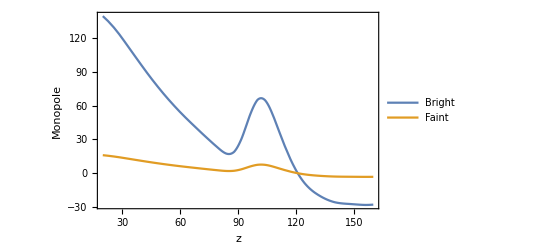

```mathematica
Plot[{d^2MonopoleBf[d],d^2MonopoleFf[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Monopole"},RotateLabel->True, ImageSize->{300},PlotLegends->{Bright, Faint}]
```

## Dipole

```mathematica
g1[z_]:=2/(r[z] HH[z])+1/2(-Omm(1+z)+2/(1+z)^2(1-Omm))/HH[z]^2
```

```mathematica
g1zSKA=Table[g1[i],{i,zSKA}]
```

{15.1422,9.64318,7.20087,5.78564,4.84435,4.16406,3.64492,3.23351,2.89842,2.61978,2.3843,2.18266,2.00812,1.85564,1.72137,1.60229,1.49603,1.40068,1.31468}

```mathematica
DipoleΛCDM=evolzSKA HzSKA(3(smodelBzSKA-smodelFzSKA)fzSKA^2 (1/(rH0zSKA HzSKA)-1)- 5(bBzSKA smodelFzSKA-bFzSKA smodelBzSKA)(1/(rH0zSKA HzSKA)-1) fzSKA+(bBzSKA-bFzSKA) g1zSKA fzSKA)
```

{24.1213,9.77788,5.65386,3.8872,2.3499,1.56104,1.09406,0.791114,0.593429,0.469213,0.398439,0.369074,0.375053,0.408054,0.457093,0.517422,0.586724,0.664253,0.748047}

```mathematica
Dipole=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA+(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{8.52762,7.57948,2.58465,1.8522,1.64075,1.59055,1.59288,1.69192,1.85435,2.07737,2.33728,2.63516,2.92011,3.15831,3.38376,3.60821,3.84616,4.10313,4.36328}

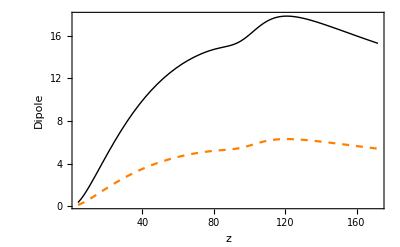

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d],d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

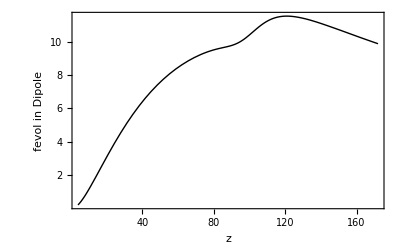

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d]-d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "fevol in Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez1[d_]:=Dipole[[1]] nu1z0[d]
```

```mathematica
WideAnglezSKA=-(2/5)(bBtildezSKA-bFtildezSKA)GtildezSKA/(rH0zSKA /H0)
```

{-0.000445278,-0.000266775,-0.000187954,-0.000142867,-0.000113461,-0.0000927289,-0.000077354,-0.0000655432,-0.0000562325,-0.0000487454,-0.0000426282,-0.0000375644,-0.000033326,-0.0000297442,-0.0000266916,-0.0000240706,-0.0000218047,-0.0000198339,-0.0000181099}

```mathematica
WideAnglez1[d_]:=WideAnglezSKA[[1]]d mu2z0[d]
```

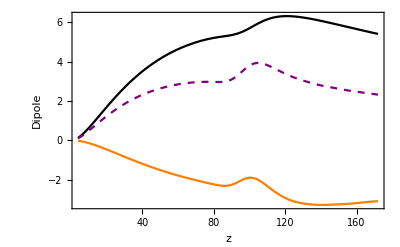

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d],  d^2(d WideAnglezSKA[[1]] mu2z0[d]),d^2Dipole[[1]] nu1z0[d]+  d^2 (d WideAnglezSKA[[1]] mu2z0[d])},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Table[Dipolez1[d],{d,4,172,4}]
```

{0.00780477,0.00679629,0.00576867,0.00491293,0.00421649,0.00364801,0.00317982,0.00279045,0.00246359,0.00218677,0.00195045,0.0017473,0.0015715,0.00141849,0.00128456,0.0011667,0.00106247,0.000969715,0.000886728,0.000812148,0.000745006,0.00068566,0.000636076,0.000597693,0.00056871,0.000544389,0.000520176,0.000494047,0.000466206,0.000437629,0.000409279,0.000381938,0.000356091,0.000331896,0.000309379,0.000288567,0.000269423,0.000251804,0.000235557,0.000220595,0.00020685,0.000194205,0.000182528}

```mathematica
Table[WideAnglez1[d],{d,4,172,4}]
```

{-0.00132914,-0.00140635,-0.00134647,-0.00125178,-0.00115108,-0.00105405,-0.000964218,-0.000882314,-0.000808364,-0.000741769,-0.000681832,-0.000627836,-0.000579184,-0.000535225,-0.000495674,-0.000459807,-0.000427538,-0.000398705,-0.000372495,-0.000348698,-0.000325254,-0.000296257,-0.000258029,-0.000217766,-0.000189832,-0.000181624,-0.000187372,-0.000196236,-0.000201817,-0.000202871,-0.000199729,-0.000193254,-0.000185034,-0.000176284,-0.000167141,-0.000157664,-0.000148471,-0.000140021,-0.000132079,-0.000124315,-0.000116917,-0.000110223,-0.000104161}

```mathematica
Abs[(Table[Dipolez1[d],{d,4,172,4}]-(Table[Dipolez1[d],{d,4,172,4}]+Table[WideAnglez1[d],{d,4,172,4}]))/(Table[Dipolez1[d],{d,4,172,4}])]
```

{0.170298,0.206929,0.233411,0.254793,0.272995,0.288937,0.303231,0.31619,0.328124,0.339208,0.349576,0.359319,0.368555,0.377319,0.38587,0.39411,0.402401,0.411157,0.420078,0.429352,0.436578,0.432076,0.405657,0.364344,0.333793,0.333629,0.360209,0.3972,0.432892,0.463569,0.488002,0.505982,0.519626,0.531144,0.540246,0.546369,0.551069,0.55607,0.560711,0.563546,0.565225,0.567559,0.570662}

```mathematica
rH0zSKA/H0
```

{433.566,704.263,960.18,1201.58,1428.95,1642.94,1844.3,2033.82,2212.29,2380.49,2539.19,2689.08,2830.84,2965.07,3092.35,3213.19,3328.07,3437.42,3541.64}

## Quadrupole

```mathematica
QuadrupoleBright=-(4 bBtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-1.48561,-1.49436,-1.48316,-1.4575,-1.42217,-1.38104,-1.3371,-1.29255,-1.24892,-1.20728,-1.16829,-1.13234,-1.09965,-1.07029,-1.04425,-1.02145,-1.00181,-0.985196,-0.971501}

```mathematica
QuadrupoleFaint=-(4 bFtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.515511,-0.550277,-0.576307,-0.594886,-0.607477,-0.615501,-0.620224,-0.622708,-0.623809,-0.624197,-0.624384,-0.624756,-0.6256,-0.627126,-0.629491,-0.632807,-0.637159,-0.642609,-0.649207}

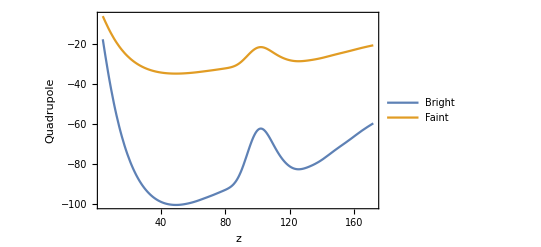

```mathematica
Plot[{d^2 QuadrupoleBright[[1]] mu2z0[d],d^2QuadrupoleFaint [[1]]mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Quadrupole"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Bright,Faint}]
```

```mathematica
QuadrupoleBz1[d_]:=QuadrupoleBright[[1]] mu2z0[d]
QuadrupoleFz1[d_]:=QuadrupoleFaint[[1]] mu2z0[d]
```

## Hexadecapole

```mathematica
Hexadecapole=(8 GtildezSKA^2/35)/Sigma8z0^2
```

{0.0723187,0.0761278,0.0779996,0.0782448,0.0772142,0.0752437,0.0726254,0.0695971,0.0663425,0.0629982,0.0596618,0.0564005,0.053258,0.0502613,0.0474248,0.0447544,0.0422501,0.0399079,0.0377213}

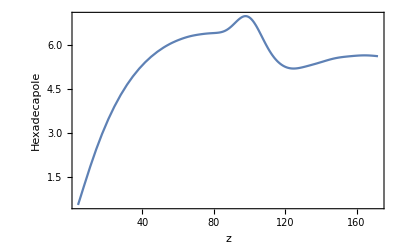

```mathematica
Plot[{d^2Hexadecapole[[1]] mu4z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Hexadecapole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Hexadecapolez1[d_]:=Hexadecapole[[1]] mu4z0[d];
```

## Octupole

```mathematica
Octupole=(HzSKA/Sigma8z0^2)2 (βBzSKA-βFzSKA)GtildezSKA^2/5
```

{0.477794,1.20863,0.29037,0.241815,0.229636,0.222303,0.213836,0.221678,0.239601,0.265522,0.295077,0.327012,0.352109,0.365447,0.373774,0.379478,0.384869,0.390778,0.395488}

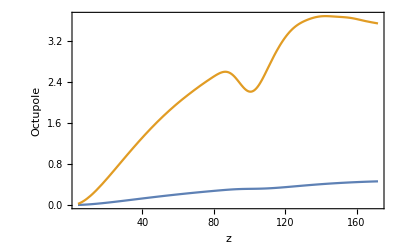

```mathematica
Plot[{d^2 Octupole[[1]] nu3z0[d], d^2 Octupole[[1]] nu3z0[d] - d^2 WideAnglezSKA[[1]]d mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Octupole"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
Octupolez1[d_]:=Octupole[[1]] nu3z0[d]
OctupoleWAz1[d_]:=Octupole[[1]] nu3z0[d] -WideAnglezSKA[[1]] d mu2z0[d]
```

## Joint plot

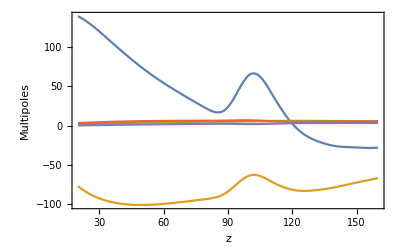

```mathematica
Plot[{d^2 MonopoleBf[d],d^2QuadrupoleBz1[d],d^2Dipolez1[d],d^2Hexadecapolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

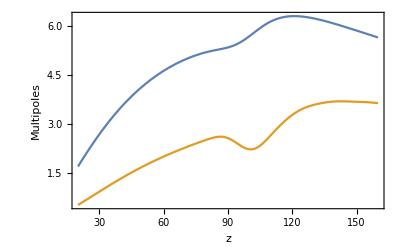

```mathematica
Plot[{d^2Dipolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

## Signal-to-noise Ratios

```mathematica
{dmin,dmax}
```

{20,160}

```mathematica
{maxsep,ktot,indist,ldist}
```

{40,19,5,36}

## Monopole

```mathematica
ξ0BSKAmatrix=Table[MonopoleBright[[k]]mu0z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ0BSKAmatrix]
```

{36,19}

```mathematica
Dimensions[varTOTMONOBrightLp4d4to172zSKA]
```

{19,43,43}

```mathematica
varξ0BTOT=Table[ varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ0BTOT=Table[Inverse[varξ0BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ0BTOT]
```

{19,36,36}

```mathematica
ξ0BSKAmatrix[[All,1]]
```

{0.348405,0.230826,0.158815,0.112449,0.0813821,0.0599209,0.044724,0.0337459,0.02567,0.0196497,0.0150695,0.0115688,0.00882682,0.0066175,0.00485786,0.00343548,0.00246272,0.00245834,0.00371665,0.00550873,0.00649228,0.00598283,0.00442899,0.00268481,0.00124052,0.000185342,-0.00051009,-0.000912054,-0.00113393,-0.00126204,-0.00131186,-0.00129275,-0.00124629,-0.00120377,-0.00115612,-0.00108847}

```mathematica
SNrSKAMonopole=Table[Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{61.6745,95.6451,124.69,148.379,166.394,178.708,185.12,185.693,180.453,169.632,154.328,135.489,114.406,92.9155,71.9188,53.1342,37.4362,25.0349,15.9606}

```mathematica
SNSKAMonopoleTotal= Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

560.717

## Dipole

```mathematica
ξ1SKAmatrix=Table[(Dipole[[k]])nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{29.1809,33.4017,13.7786,9.43824,7.53903,6.43662,5.56163,5.01749,4.59381,4.22383,3.85021,3.46349,3.01059,2.51603,2.03324,1.59799,1.22106,0.898881,0.631878}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

49.9104

```mathematica
1-54.6434/78.2865
```

0.302007

## Dipole + WA

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d]+d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{20.4742,26.4045,7.42313,4.78971,4.17571,3.99265,3.79027,3.73498,3.67001,3.56357,3.38034,3.13155,2.77834,2.35487,1.92336,1.52434,1.1728,0.868296,0.613243}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

36.405

## Quadrupole

```mathematica
ξ2BSKAmatrix=Table[QuadrupoleBright[[k]]mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ2BSKAmatrix]
```

{36,19}

```mathematica
varξ2BTOT=Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ2BTOT=Table[Inverse[varξ2BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ2BTOT]
```

{19,36,36}

```mathematica
ldist
```

36

```mathematica
SNrSKAQuadrupole=Table[Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{29.384,47.4871,63.6857,77.1166,87.1639,93.551,96.0596,94.766,89.8592,81.7676,71.4804,59.8932,47.9973,36.8671,26.9319,18.7811,12.5047,7.91341,4.78116}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

275.896

## Octupole

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
Octupole[[1;;ktot]]
```

{0.477794,1.20863,0.29037,0.241815,0.229636,0.222303,0.213836,0.221678,0.239601,0.265522,0.295077,0.327012,0.352109,0.365447,0.373774,0.379478,0.384869,0.390778,0.395488}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupole=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{2.00275,6.15343,1.55342,1.21317,1.03245,0.876751,0.724663,0.634969,0.569667,0.513708,0.457331,0.398477,0.330276,0.25881,0.194095,0.140559,0.0985411,0.066402,0.0427236}

```mathematica
SNSKAOctupoleTotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

7.0519

```mathematica
1-4.68151/8.50621
```

0.449636

## Octupole + WA

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d] -d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupoleWA=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{13.6809,14.7373,8.11954,5.90328,4.37163,3.27139,2.44229,1.86607,1.4475,1.13423,0.893468,0.702084,0.538986,0.400639,0.288373,0.201901,0.137418,0.0901558,0.0566663}

```mathematica
SNSKAOctupoleWATotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

23.445

## Hexadecapole

```mathematica
ξ4TSKAmatrix=Table[Hexadecapole[[k]]mu4z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ4TSKAmatrix]
```

{36,19}

```mathematica
varξ4TTOT=Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ4TTOT=Table[Inverse[varξ4TTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ4TTOT]
```

{19,36,36}

```mathematica
SNrSKAHexadecapole=Table[Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{9.7378,15.1786,19.6006,22.8466,24.8844,25.783,25.6376,24.5914,22.7903,20.396,17.6385,14.7113,11.8091,9.1342,6.76497,4.8075,3.27383,2.12239,1.3088}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

74.4918

## Plot

```mathematica
SNSKAz015Dipole=Table[ξ1SKAmatrix[[m,1]]/Sqrt[varξ1TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Monopole=Table[ξ0BSKAmatrix[[m,1]]/Sqrt[varξ0BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Quadrupole=Table[Abs[ξ2BSKAmatrix[[m,1]]]/Sqrt[varξ2BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Octupole=Table[Abs[ξ3SKAmatrix[[m,1]]]/Sqrt[varξ3TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Hexadecapole=Table[Abs[ξ4TSKAmatrix[[m,1]]]/Sqrt[varξ4TTOT[[1,m,m]]],{m,1,ldist}];
```

```mathematica
ds=Table[d,{d,dmin,dmax,4}];
```

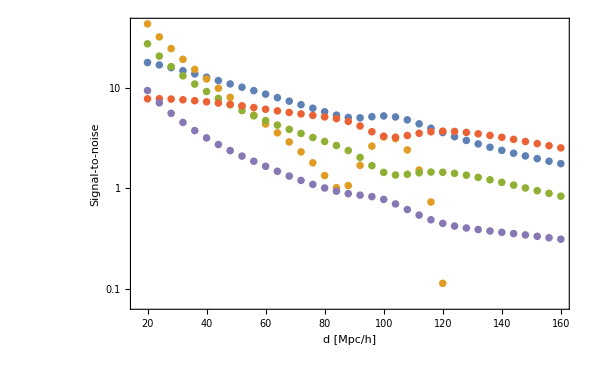

```mathematica
ListLogPlot[{Table[{ds[[i]], SNSKAz015Dipole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Monopole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Quadrupole[[i]]},{i,1,ldist}], Table[{ds[[i]], SNSKAz015Octupole[[i]]},{i,1,ldist}],
Table[{ds[[i]], SNSKAz015Hexadecapole[[i]]},{i,1,ldist}]},PlotRange->Full,PlotStyle->{•},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Signal-to-noise"},RotateLabel->True]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
(*Export["CovarianceMatrixzSKA_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]*)
```

```mathematica
(*Export["CovarianceMatrix_P_at_z"<>ToString[zSKA[[1]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA[[1]],"Table","FieldSeparators"->" ",OverwriteTarget->True]*)
```

```mathematica
nBSKA
```

1/10

```mathematica
nFSKA
```

9/10

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

EXPORT - WITH OCTUPOLE

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixOCTtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
nBSKA
```

1/10

```mathematica
nFSKA
```

9/10

```mathematica
Exit[]
```